```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
```

```mathematica
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,RGBColor[0.01, 0.61, 0.]};
```

Guardar y cargar estado

```mathematica
SaveKernelState[path_:FileNameJoin[{NotebookDirectory[],StringJoin[FileBaseName[NotebookFileName[]],"_state.mx"]}]]:=DumpSave[path,"Global`"];
LoadKernelState[path_:FileNameJoin[{NotebookDirectory[],StringJoin[FileBaseName[NotebookFileName[]],"_state.mx"]}]]:=Get[path];
```

```mathematica
SaveKernelState[]
```

{Global`}

## Chi squared

```mathematica
testData = RandomVariate[BinomialDistribution[10,0.3],100]
```

{6,5,3,5,3,2,5,1,3,4,4,3,2,5,2,4,5,1,2,3,3,3,3,4,4,3,4,2,5,4,1,4,3,3,4,3,1,3,3,4,1,0,3,5,1,1,5,4,4,3,3,4,3,2,3,4,0,4,1,4,2,2,4,3,1,5,4,2,3,5,5,2,5,3,2,6,4,1,3,3,2,5,4,3,3,1,5,2,2,2,3,3,2,4,0,1,3,3,2,3}

```mathematica
Oi = N[Map[Count[testData,#]&,Range[0,Max[testData]]]/Length[testData]]
```

{0.4998,0.2482,0.1229,0.0679,0.0297,0.0154,0.0075,0.0046,0.0018,0.0014,0.0005,0.0001,0.0001,0.,0.,0.0001}

```mathematica
Total[Oi]
```

1.

```mathematica
Ei = Map[PDF[GeometricDistribution[0.5],#]&,Range[0,Max[testData]]]
```

{0.5,0.25,0.125,0.0625,0.03125,0.015625,0.0078125,0.00390625,0.00195313,0.000976563,0.000488281,0.000244141,0.00012207,0.0000610352,0.0000305176,0.0000152588}

```mathematica
Total[(Oi-Ei)^2/Ei]
```

0.00157786

```mathematica
RandomXiSquare[n_,dist_]:=Block[{testData,Oi,Ei},
testData = RandomVariate[dist,n];
Oi = N[Map[Count[testData,#]&,Range[0,Max[testData]]]/n];
Ei = Map[PDF[dist,#]&,Range[0,Max[testData]]];
Total[(Oi-Ei)^2/Ei]
];
```

```mathematica
xi2s = ProgressTable[RandomXiSquare[100,BinomialDistribution[10,0.3]],50000];
```

```mathematica
FindDistribution[xi2s,5]
```

{MixtureDistribution[{0.274586,0.725414},{NormalDistribution[0.0056536,0.0357728],LogNormalDistribution[-2.15625,0.61284]}],MixtureDistribution[{0.276388,0.723612},{NormalDistribution[0.0120689,0.0349399],CauchyDistribution[0.116825,0.032447]}],MixtureDistribution[{0.982977,0.0170227},{NormalDistribution[0.0882954,0.0695565],NormalDistribution[3.89947,6.59109]}],StudentTDistribution[0.0898999,0.0576861,2.76005],MixtureDistribution[{0.267984,0.732016},{LogisticDistribution[0.0141592,0.0155974],LogNormalDistribution[-2.16665,0.618153]}]}

```mathematica
xi2s[[1;;20]]
```

{0.00730604,0.0771277,0.0683291,0.0401889,0.0289163,0.079928,0.211053,0.0400364,0.0104389,0.0465786,0.833533,0.0862198,0.0689971,0.0851458,0.0297079,0.0615297,0.0466739,0.0339138,0.240233,0.0225935}

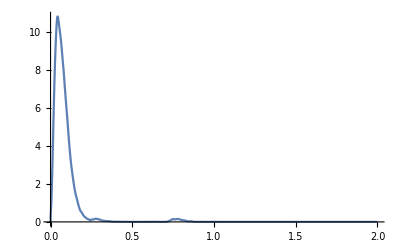

```mathematica
SmoothHistogram[xi2s,PlotRange->{{0,2},All}]
```

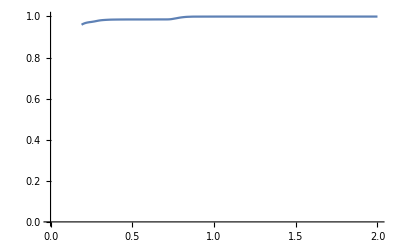

```mathematica
SmoothHistogram[xi2s,Automatic,"CDF",PlotRange->{{0,2},{0,1}}]
```

```mathematica
FindDistributionParameters[xi2s,ChiSquareDistribution[v]]
```

{v→0.61055}

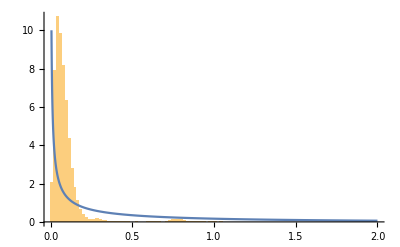

```mathematica
Show[
Histogram[xi2s,Automatic,"PDF",PlotRange->{{0,2},All}],
Plot[PDF[ChiSquareDistribution[0.6105502004401794],x],{x,0,2},PlotRange->{0,10}]
]
```

## Anderson-Darling y Cramer-von-mises

```mathematica
PEstimator[data_,class_]:=N[Count[data,class]/Length[data]];
ModelP[j_]:=PDF[GeometricDistribution[0.5],j];
```

```mathematica
Z[data_,j_]:=Sum[Count[data,i],{i,0,j}]-Length[data]*Sum[ModelP[j],{i,0,j}];
```

```mathematica
GeometricCramerVonMisesTest[data_]:=(1/Length[data])Sum[Z[data,j]^2*ModelP[j],{j,0,Max[data]}];
```

```mathematica
Options[Parallelize]
```

{DistributedContexts:>$Context,Method→Automatic}

```mathematica
ProgressParallelTable[Labeled[Framed[i],$KernelID],{i,10},Method->"CoarsestGrained"]
```

{11,21,32,42,53,63,74,85,96,107}

```mathematica
vonMises = ProgressParallelTable[GeometricCramerVonMisesTest[RandomVariate[GeometricDistribution[0.5],20000]],150000];
```

```mathematica
pvalList = ProgressTable[{pVal,Quantile[vonMises,1-pVal]},{pVal,0.000001,1,0.00001}];
```

```mathematica
testScoreToPValuePts = Map[Reverse,pvalList];
```

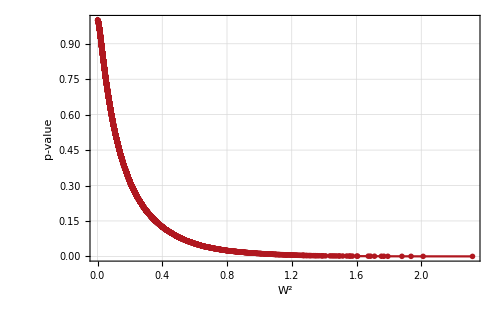

```mathematica
ListLinePlot[testScoreToPValuePts,
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["W^2",15], Style["p-value",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->Automatic,
PlotStyle->First[colors]
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"testScoreToPValuePts.csv"}],testScoreToPValuePts]
```

C:\Users\hp\Documents\Programacion\TrendDurationAnalysis\testScoreToPValuePts.csv

```mathematica
ListLinePlot[testScoreToPValuePts,
PlotRange->All,
ScalingFunctions->"Log",
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["W^2",15], Style["p-value",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->Automatic,
PlotStyle->First[colors]
]
```

-Graphics-

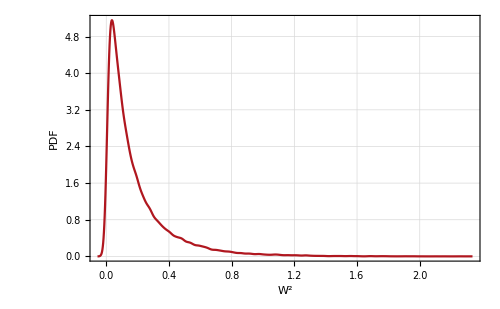

```mathematica
SmoothHistogram[vonMises,
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["W^2",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->Automatic,
PlotStyle->First[colors]
]
```

```mathematica
FindDistribution[vonMises,5]
```

{MixtureDistribution[{0.863635,0.136365},{BetaDistribution[1.25875,8.85581],LogNormalDistribution[-0.69818,0.480676]}],LogNormalDistribution[-2.23767,1.12852],MixtureDistribution[{0.852558,0.147442},{BetaDistribution[1.18323,7.93005],GammaDistribution[2.11824,0.24095]}],MixtureDistribution[{0.856033,0.143967},{HalfNormalDistribution[8.18272],LogNormalDistribution[-0.681645,0.446979]}],ExponentialDistribution[5.18539]}